# TD

play

```mathematica
Np=2000
k=1.38x10^-23
me=9.109x10^-31
hbar=1.055x10^-34
ec=1.602x10^-19
Uh=13.6*ec
```

2000

1.38/x10^23

9.109/x10^31

1.055/x10^34

1.602/x10^19

21.7872/x10^19

```mathematica
tc=(2*Pi*me*k/(hbar^2))^(3/2)
sh[x_,T_,V_]:=x^2-(1-x)*V*T^(3/2)*Exp[-Uh/(k*T)]
```

597.774 (x10^14)^(3/2)

```mathematica
ans=Solve[sh[x,T,1]== 0,x]
```

{{x→0.5 (-1. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)-1. √(4. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.5757 x10^4)/T) T^3))},{x→0.5 (-1. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+√(4. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.5757 x10^4)/T) T^3))}}

```mathematica
Solve[sh[x,200,1],x]
```

```mathematica
ans[[1]]
```

```mathematica
sh[x,100,1]
```

Solve::naqs: -1000 ⅇ^(-0.157878 x10^4) (1-x)+x^2 is not a quantified system of equations and inequalities.

Solve::naqs: A (1-x)+x^2 is not a quantified system of equations and inequalities.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

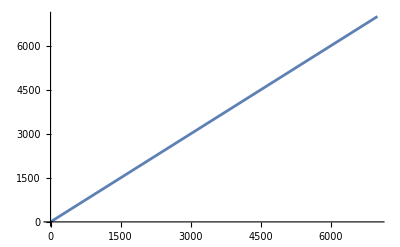

```mathematica
Plot[T/. Solve[sh[x,T]==0.06366,x],{T,0,7000}]
```

```mathematica
Evaluate[T->100,ans[[1]]]
```

Sequence[T→100,{x→0.5 (-1. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)-1. √(4. ⅇ^(-(15.7878 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.5757 x10^4)/T) T^3))}]

```mathematica
nx[T_]:= 0.5 (-1. ⅇ^(-(15.787826086956526 x10^4)/T) T^(3/2)-1. √(4. ⅇ^(-(15.787826086956526 x10^4)/T) T^(3/2)+1. ⅇ^(-(31.575652173913053 x10^4)/T) T^3))
```

```mathematica
Table[Simplify[Evaluate[nx[100]]],1]
```

{-500. ⅇ^(-0.157878 x10^4)-0.5 √(1.×10^6 ⅇ^(-0.315757 x10^4)+4000. ⅇ^(-0.157878 x10^4))}